```mathematica
Lead[m_]:=Lead[m]=ParallelTable[ToExpression[Import["/home/shardulmukim/PhD/fwi/AGNR/leads/size_"<>ToString[m]<>"_lead_"<>ToString[x]<>"_.dat"]],{x,Range[-3,3,0.01]}]
```

```mathematica
Clear[Lead]
```

```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=
ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[2m],Join[Table[{i,i-1},{i,Range[2,2m,1]}],Table[{i,i+1},{i,Range[1,2m,1]}],Table[{2n-1,2m-2n+2},{n,(m+1)/2}],Table[{2m-2n+2,2n-1},{n,(m-1)/2}]]->t]
```

```mathematica
T1[t_,m_]:=T1[t,m]=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2m-2n+1},{n,(m-1)/2}]->t]
```

```mathematica
Clear[LEFT]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=Lead[m][[Round[ω*100+301]]](* Module[{unit=Inverse[β[ω,δ,t,ϵ,51]],J=Inverse[β[ω,δ,t,ϵ,51]]},Do[J= Inverse[IdentityMatrix[102]-unit.T1[t,51].J.T1[t,51]].unit,x];J=J]*)
```

```mathematica
LEFT[0,0.0001,1,0,25]
```

{{0.-0.0000825962 ⅈ,0.585198+0. ⅈ,0.+0.0000240764 ⅈ,-0.252118+0. ⅈ,0.+1.13534×10^-6 ⅈ,0.0469656+0. ⅈ,39,0.205152+0. ⅈ,0.-0.0000318845 ⅈ,-0.33308+0. ⅈ,0.+0.000041116 ⅈ,0.414802+0. ⅈ},{1},47,{1}}
 |  |  |  |

```mathematica
(*leadgenerateleft[ω_,δ_,t_,ϵ_,m_]:= leadgenerateleft[ω,δ,t,ϵ,m]= Module[{unit=Inverse[β[ω,δ,t,ϵ,m]],J=Inverse[β[ω,δ,t,ϵ,m]]},Do[J= Inverse[IdentityMatrix[2m]-unit.T1[t,m].J.T1[t,m]].unit,150000];J=J]*)
```

```mathematica
(*leadgenerateleft[0,0.0001,1,0,51]*)
```

```mathematica
ρ[t_,m_]:=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2n},{n,(m-1)/2}]->t]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
SR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-g[ω,δ,t,ϵ,m].ConjugateTranspose[T1[t,m]].LEFT[ω,δ,t,ϵ,m].T1[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-LEFT[ω,δ,t,ϵ,m].ρ[t,m].LEFT[ω,δ,t,ϵ,m].ρ[t,m]].LEFT[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-LEFT[ω,δ,t,ϵ,m].ρ[t,m].LEFT[ω,δ,t,ϵ,m].ρ[t,m]].LEFT[ω,δ,t,ϵ,m]
```

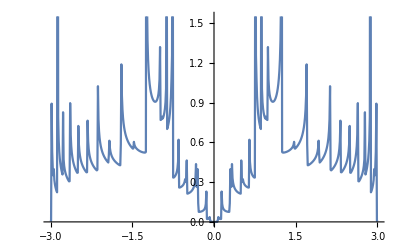

```mathematica
ListLinePlot[Table[{ω,-Im[IL[ω,0.0001,1,0,25][[14,14]]]},{ω,Range[-3,3,0.01]}]]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,t,ϵ,m].ρ[t,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:=Abs[Tr[gdd[ω,δ,t,ϵ,m].ρ[t,m].grr[ω,δ,t,ϵ,m].ρ[t,m]-ρ[t,m].GNON[ω,δ,t,ϵ,m].ρ[t,m].GNON[ω,δ,t,ϵ,m]]]
```

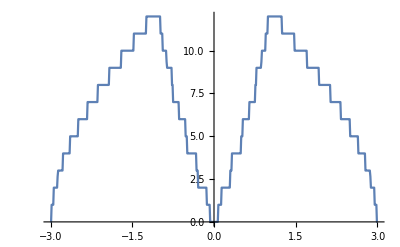

```mathematica
Table[{ω,tr[ω,0.0001,1,0,25]},{ω,Range[-3,3,0.01]}]//ListLinePlot
```

```mathematica
TLD[t_,m_]:=Module[{sizeoflead=13},Module[{mat=RandomInteger[0,{50,50}]},ReplacePart[mat,Table[{2n,50-2n+1},{n,(m-1)/2}]->t]]]
```

```mathematica
ρLD[t_,m_]:=Module[{sizeoflead=13},Module[{mat=RandomInteger[0,{50,50}]},ReplacePart[mat,Table[{2n,2n},{n,(m-1)/2}]->t]]]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ,25]]
```

```mathematica
Clear[SLLEAD]
```

```mathematica
SLLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;26,1;;26]]=LEFT[ω,0.0001,1,0,13];MAT]
```

```mathematica
SRLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;2m,1;;2m]]=LEFT[ω,0.0001,1,0,m];MAT]
```

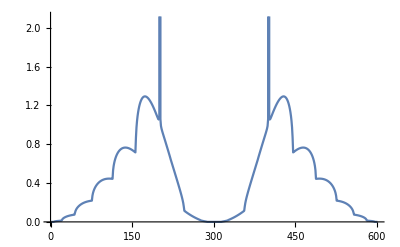

```mathematica
ListLinePlot[Table[-Im[SRLEAD[Ω,13][[1,1]]],{Ω,Range[-3,3,0.01]}]]
```

```mathematica
device1[ω_]:=Module[{sizeoflead=13},Inverse[IdentityMatrix[50]-g[ω,0.0001,1,0].ConjugateTranspose[TLD[1,13]].SLLEAD[ω,13].TLD[1,13]].g[ω,0.0001,1,0]]
```

```mathematica
f1[y_,start_,stop_]:= Table[{x,y},{x,start,stop}]
```

```mathematica
s[xstart_,xstop_,ystart_,ystop_]:=Module[{J=f1[ystart,xstart,xstop]},Do[J=Join[f1[y,xstart,xstop],J],{y,ystart+1,ystop}];J=J]
```

```mathematica
Clear[dist]
```

```mathematica
dist[total_,concentration_]:=dist[total,concentration]=Table[SortBy[Join[RandomSample[Join[s[1,50,1,12],s[1,50,38,50](*,s[38,50,38,50]*)],concentration],RandomSample[Join[s[1,50,13,37](*,s[38,50,1,37]*)],total-concentration]],First],10000]
```

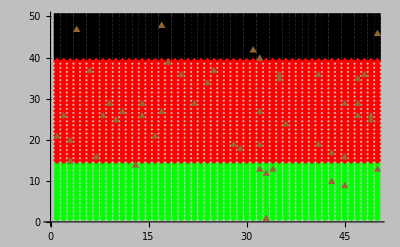

```mathematica
ListPlot[{s[1,50,1,14],s[1,50,40,50],s[1,50,15,39],dist[50,10][[515]]},PlotStyle->{Green,Black,Red,Brown},Background->Lighter[Gray, 0.5],PlotMarkers->Automatic]
```

```mathematica
dist[50,20][[1]]
```

{{1,35},{2,21},{5,36},{6,2},{6,24},{7,13},{7,25},{7,27},{7,38},{8,16},{8,48},{9,35},{9,45},{11,10},{11,23},{11,30},{12,2},{12,36},{12,46},{14,12},{14,33},{14,36},{15,32},{15,36},{16,12},{16,14},{16,29},{18,35},{25,13},{25,43},{29,7},{29,26},{30,33},{32,16},{35,21},{37,45},{39,5},{39,6},{39,33},{40,18},{41,25},{43,8},{44,37},{44,39},{45,10},{47,50},{48,17},{48,48},{50,26},{50,39}}

```mathematica
f[ω_,δ_,t_,ϵ_,ϵ1_,unitcell_,total_,concentration_,number_]:=Module[{J=β[ω,δ,t,ϵ,25],abc=dist[total,concentration][[number]]},Do[J=Module[{m=unitcell},If[abc[[loc1,1]]==m,ReplacePart[J,{{abc[[loc1,2]],abc[[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]
```

```mathematica
CA[ω_,δ_,t_,ϵ_,ϵ1_,m_,total_,concentration_,number_]:=Module[{SSL=SRLEAD[ω,13],Tin=T1[1,25],T=ρLD[1,13],abc=dist[total,concentration][[number]]},
sl1= Module[{J1=device1[ω]},
Do[
J1=Inverse[IdentityMatrix[2*m]-Inverse[Module[{J=β[ω,δ,t,ϵ,m]},Do[J=Module[{mm=unitcell},If[abc[[loc1,1]]==mm,ReplacePart[J,{{abc[[loc1,2]],abc[[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]].ConjugateTranspose[Tin].J1.Tin].Inverse[Module[{J=β[ω,δ,t,ϵ,m]},Do[J=Module[{mm=unitcell},If[abc[[loc1,1]]==mm,ReplacePart[J,{{abc[[loc1,2]],abc[[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]],{unitcell,50}];J1=J1];
Il1:=Inverse[IdentityMatrix[2*m]-sl1.T.SSL.T].sl1;
Ir1:=Inverse[IdentityMatrix[2*m]-SSL.T.sl1.T].SSL;
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:=SSL.T.Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
tra=Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]];
{tra,If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,0.0001,1,0,15],tr[ω,0.0001,1,0,15],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]}]
```

```mathematica
CA[1.5,0.0001,1,0,0,25,50,15,1]//MatrixForm
```

(2.92817
2.92817)

```mathematica
CA[1,0.0001,1,0,1,29,50,15,1]
```

10.8179

```mathematica
Table[Mean[ParallelTable[CA[1.7,0.0001,1,0,1,25,x,x/2,n],{n,500}]],{x,Range[10,100,10]}]
```

{{2.63506,2.63506},{2.23679,2.23679},{1.9123,1.9123},{1.65278,1.65278},{1.42992,1.42992},{1.25574,1.25574},{1.10521,1.10521},{0.920893,0.920893},{0.84052,0.84052},{0.725301,0.725301}}

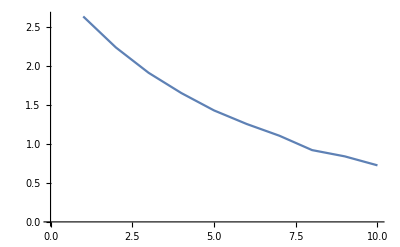

```mathematica
ListLinePlot[Transpose[%214][[1]]]
```

```mathematica
Table[{ω,Mean[ParallelTable[CA[ω,0.0001,1,0,1,29,100,57,n],{n,500}]]},{ω,Range[1,3,0.01]}]
```

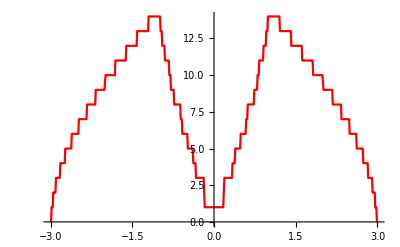

```mathematica
ListLinePlot[Table[{ω,CA[ω,0.0001,1,0,0,29,50,20,1]},{ω,Range[-3,3,0.01]}],PlotStyle->Red]
```

```mathematica
Table[Export["/home/shardulmukim/PhD/fwi/AGNR/sudo_q/CA_HALF_DEIVE_25agnr_50imp_lead_13agnr_sameside_"<>ToString[x]<>"_.dat",Print[x];Table[{ω,Mean[ParallelTable[CA[ω,0.0001,1,0,1,25,50,x,n][[2]],{n,500}]]},{ω,Range[0,3,0.01]}]],{x,Range[10,40,5]}]
```

{/home/shardulmukim/PhD/fwi/AGNR/sudo_q/CA_HALF_DEIVE_25agnr_50imp_lead_13agnr_sameside_10_.dat,/home/shardulmukim/PhD/fwi/AGNR/sudo_q/CA_HALF_DEIVE_25agnr_50imp_lead_13agnr_sameside_15_.dat,/home/shardulmukim/PhD/fwi/AGNR/sudo_q/CA_HALF_DEIVE_25agnr_50imp_lead_13agnr_sameside_20_.dat,/home/shardulmukim/PhD/fwi/AGNR/sudo_q/CA_HALF_DEIVE_25agnr_50imp_lead_13agnr_sameside_25_.dat,/home/shardulmukim/PhD/fwi/AGNR/sudo_q/CA_HALF_DEIVE_25agnr_50imp_lead_13agnr_sameside_30_.dat,/home/shardulmukim/PhD/fwi/AGNR/sudo_q/CA_HALF_DEIVE_25agnr_50imp_lead_13agnr_sameside_35_.dat,/home/shardulmukim/PhD/fwi/AGNR/sudo_q/CA_HALF_DEIVE_25agnr_50imp_lead_13agnr_sameside_40_.dat}

```mathematica
transmission:=transmission= Table[{x,Import["/home/shardulmukim/PhD/fwi/AGNR/sudo_q/CA_HALF_DEIVE_25agnr_50imp_lead_13agnr_sameside_"<>ToString[x]<>"_.dat"]},{x,Range[10,40,5]}]
```

```mathematica
transmission1:=Table[Import["~/Downloads/PhD_new/PhD/fwi/AGNR/sudo_q/CA_HALF_DEIVE_25agnr_50imp_lead_13agnr_sameside_"<>ToString[x]<>"_.dat"],{x,Range[10,40,5]}]
```

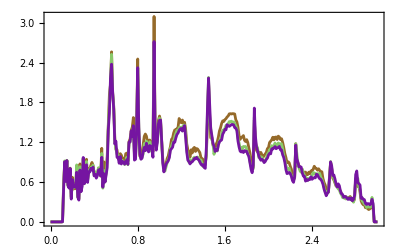

```mathematica
Show[Table[ListLinePlot[transmission1[[x]],Frame->True,PlotStyle->RandomColor[x]],{x,1,5,2}]]
```

```mathematica
input=Table[ParallelTable[{ω,CA[ω,0.0001,1,0,1,25,50,30,n][[2]]},{ω,Range[0,3,0.01]}],{n,100}]
```

{{{0.,1.08×10^-6},{0.01,1.09341×10^-6},{0.02,1.13562×10^-6},{0.03,1.21325×10^-6},{0.04,1.34012×10^-6},{0.05,1.54363×10^-6},{0.06,1.8809×10^-6},{0.07,2.48506×10^-6},{0.08,3.72847×10^-6},{0.09,7.02335×10^-6},{0.1,0.0000223412},{0.11,0.00192721},{0.12,0.325346},{0.13,0.999994},274,{2.88,0.0354904},{2.89,0.185827},{2.9,0.15672},{2.91,0.237215},{2.92,0.0282854},{2.93,0.18795},{2.94,0.508161},{2.95,0.211492},{2.96,0.0612202},{2.97,0.0000351193},{2.98,7.40804×10^-6},{2.99,3.16024×10^-6},{3.,1.76259×10^-6}},98,{1}}
 |  |  |  |

```mathematica
misfit[x_,y_,n_]:=Module[{m5=input[[n]]},
ρ1=Table[{transmission[[con,1]],1*Module[{B1=Transpose[{m5[[1;;301]][[;;,1]],(m5[[1;;301,2]]-transmission[[con,2]][[1;;301,;;]][[;;,2]])^2}]},NIntegrate[Interpolation[B1][ω],{ω,y,x}]/((x-y))]},{con,7}];lista=ρ1(*,ρ2,ρ3,ρ4*)(*,ρ5,ρ6*);
{lista,lista[[Position[lista,Min[lista]][[1,1]]]]}]
```

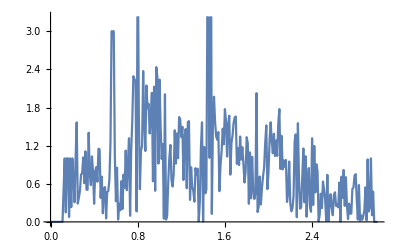

```mathematica
ListLinePlot[input[[10]]]
```

```mathematica
Table[N[Abs[Mean[Table[N[Abs[misfit[x+0.3,x,n][[2]][[1]]]],{x,Range[1,2.7,0.02]}]]-30]/30],{n,100}]//Mean
```

0.189186

```mathematica
2.46*25
```

61.5